TP 1 : Pierre-feuille-ciseaux

Travail en séance : 2G3TP5
Weidle Rémi & LANFREDI Camille

## Simulation d’une chaîne de Markov

Question 1.

Définition de la matrice P  et de la liste vide A:

```mathematica
(* Matrice P *)
P={{0.8,0.1,0.1},{0.3,0.4,0.3},{0.1,0.1,0.8}};
MatrixForm[P]
(* Liste Vide A*)
A={}
```

(0.8 | 0.1 | 0.1
0.3 | 0.4 | 0.3
0.1 | 0.1 | 0.8)

{}

Question 2.

A. La fonction utilise un chiffre aléatoire entre 0 et 1 pour choisir uniformément un chiffre entre 1, 2 et 3. Cela permet de garantir que chaque coup a une probabilité égale d’être choisi.  Caractéristique d’une loi uniforme.

B.

```mathematica
randomPFSuniform[]= Ceiling[3*RandomReal[]]
```

1

Question 3.

La fonction AppendTo permet de ranger le chiffre aléatoire dans A :

```mathematica
AppendTo[A,randomPFSuniform[]]
```

{1,1,1}

Question 4.

Le module compare rand à a et a+b, puis renvoie : 1, 2 ou 3.

```mathematica
randomPFS[a1_,b1_]:=Module[{randomNumber},randomNumber=RandomReal[];
If[randomNumber<a1,Return[1]];
If[randomNumber<a1+b1,Return[2]];
Return[3];]
randomPFS[0.1,0.8]

(* Coefficients de la matrice : [0.1 ; 0.8] donc 0 et 1 sont exclus
```

2

Question 5.

La boucle 'for' permet de remplir la liste A de 100 échantillons de tirages aléatoires.

```mathematica
A={randomPFSuniform[]};
Do[state = A[[-1]];
AppendTo[A,randomPFS[P[[state,1]],P[[state,2]]]],{99}]
A
```

{1,1,2,3,3,3,3,3,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,3,3,3,3,2,3,3,3,3,3,1,2,1,1,1,1,1,1,1,1,1,1,3,2,3,3,1,2,1,1,3,3,3,3,2,1,1,1,1,1,1,1,1,3,3,3,3,1,1,1,1,1,1,3,3,3,1,2,2,1,2,3,3,3,3,3,2}

Question 6.

Omniprésence du coup 1 :  La probabilité de rester dans l'état 1 est élevée (0.8), d'ou son omniprésence .

Alternance entre les états 1 et 2 : Les probabilités de transition entre l'état 1 et l'état 2 (0.1)
et entre l'état 2 et l'état 1 (0.3)  sont non négligeables. Cela peut expliquer pourquoi il y a une alternance entre ces deux états dans la séquence A.

Présence moins fréquente de l'état 3 : Bien que la probabilité de rester dans l'état 3 soit élevée (0.8), les probabilités de transition depuis et vers l'état 3 sont relativement faibles par rapport aux transitions entre les états 1 et 2. Cela peut expliquer pourquoi l'état 3 est observé moins fréquemment dans la séquence A.

Ces observations montrent comment la structure de la matrice  P influence la séquence de coups générée. Les probabilités plus élevées favorisent certaines transitions, ce qui se reflète dans  l'observation des différents coups.

## Implémentation du jeu

Question 7.

```mathematica
(*Règles du jeu *)
dico[1]="Pierre";
dico[2]="Feuille";
dico[3]="Ciseaux";
regle[1,3]=regle[3,2]=regle[2,1]=1;(*coups gagnants*)
regle[3,1]=regle[2,3]=regle[1,2]=-1;(*coups perdants*)
regle[a_,a_]=0; (*coups nuls*)
```

```mathematica
(*Initialisation*)
coupsHumain={};
victoires={};
message ="À vous de jouer";
```

```mathematica
(* Programmation du jeu*)
Jouer[a_]:= Module[{coupMachine},
(*Prise de décision de l'ordinateur*)
(* Question 7.A*)
coupMachine=randomPFSuniform[];

(* Sauvegarde du coup de l'humain *)
AppendTo[coupsHumain,a];
(* À compléter à la question 8 *)

(*Affichage du choix de l'ordinateur et du résultat*)
message = "Humain: "<>dico[coupsHumain⟦-1⟧]<>"|Machine: "<>dico[coupMachine]<>"|Gain pour l'humain: "<>ToString[regle[coupsHumain⟦-1⟧,coupMachine]];

(*Sauvegarde du résultat*)
AppendTo[victoires,regle[coupsHumain[[-1]],coupMachine]];
]
```

```mathematica
(*Interface Homme-Machine*)
ButtonBar[{"Pierre":> Jouer[1],"Feuille":>Jouer[2],"Ciseaux":>Jouer[3]}]
Dynamic[message]
(*Affichage des résultats*)
Dynamic[ListPlot[Accumulate[victoires]/Range[Length[victoires]],Joined->True]]
Dynamic[100.0*Mean[victoires]]
```

Pierre | Feuille | Ciseaux

7.B. 
Le graphique ci-dessus, affiche la moyenne des gains du jeu (Défaite '-1', Match nul '0', et Victoire '1').
L’espérance du jeu est de 0,25 , soit quasiment 0. Donc, la moyenne tend également vers 0.

Question 8.

```mathematica
(*Règles du jeu *)
dico[1]="Pierre";
dico[2]="Feuille";
dico[3]="Ciseaux";
regle[1,3]=regle[3,2]=regle[2,1]=1;(*coups gagnants*)
regle[3,1]=regle[2,3]=regle[1,2]=-1;(*coups perdants*)
regle[a_,a_]=0; (*coups nuls*)

(*Initialisation*)
Mem = ConstantArray[0,{3,3}];
MatrixForm[Mem]
coupsHumain={};
victoires={};
message ="À vous de jouer";randomPFSuniform[]
(* Question 8 B*)


(* Programmation du jeu*)
(* Question 8 A*)
Jouer2[a_]:= Module[{coupMachine},
(*Prise de décision de l'ordinateur*)
coupMachine=randomPFSuniform[];

(* Sauvegarde du coup de l'humain *)
AppendTo[coupsHumain,a];

(* À compléter à la question 8 *)
(*Vérification de l'historique -> si coups>1*)
If[Length[coupsHumain]>1,
dernierCoup=Last[coupsHumain];(*Nous récupérons le dernier coup joué par l'Humain*)
avDernierCoup=coupsHumain[[-2]];(*Nous récupérons l'avant  dernier coup joué par l'Humain*)

(*Mettre à jour la matrice Mem*)
Mem[[avDernierCoup,dernierCoup]]+=1;]

(*Affichage du choix de l'ordinateur et du résultat*)
message = "Humain: "<>dico[coupsHumain⟦-1⟧]<>"|Machine: "<>dico[coupMachine]<>"|Gain pour l'humain: "<>ToString[regle[coupsHumain⟦-1⟧,coupMachine]];

(*Sauvegarde du résultat*)
AppendTo[victoires,regle[coupsHumain[[-1]],coupMachine]];
]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

3

```mathematica
(*Interface Homme-Machine*)
ButtonBar[{"Pierre":> Jouer[1],"Feuille":>Jouer[2],"Ciseaux":>Jouer[3]}]
Dynamic[message]
(*Affichage des résultats*)
Dynamic[ListPlot[Accumulate[victoires]/Range[Length[victoires]],Joined->True]]
Dynamic[100.0*Mean[victoires]]
(* Question 8 D*)
Dynamic[Mem]
Dynamic[MatrixForm[Mem]]
```

Pierre | Feuille | Ciseaux

Question 9.

```mathematica
(*Règles du jeu *)
dico[1]="Pierre";
dico[2]="Feuille";
dico[3]="Ciseaux";
regle[1,3]=regle[3,2]=regle[2,1]=1;(*coups gagnants*)
regle[3,1]=regle[2,3]=regle[1,2]=-1;(*coups perdants*)
regle[a_,a_]=0; (*coups nuls*)
```

```mathematica
(*Initialisation*)
g = {0,0,0}; 
Mem = ConstantArray[0,{3,3}];
MatrixForm[Mem]
coupsHumain={};
victoires={};
message ="À vous de jouer";randomPFSuniform[]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

1

```mathematica
(* Programmation du jeu*)
(*Question 9 A*)
Jouer3[a_]:= Module[{coupMachine},

(*Question 9 B.  Calcul des gains pour les coups précédents de l'humain*)
         g[[1]]=Mem[[coupsHumain[[-1]],3]]-Mem[[coupsHumain[[-1]],2]];
         g[[2]]=Mem[[coupsHumain[[-1]],1]]-Mem[[coupsHumain[[-1]],3]];
         g[[3]]=Mem[[coupsHumain[[-1]],2]]-Mem[[coupsHumain[[-1]],1]];
;
(*Question 9.C Prise de décision de l'ordinateur*)
coupMachine=Ordering[g,-1][[1]];(*L'ordinateur choisit son coup en fonction des valeurs de g*)

(* Sauvegarde du coup de l'humain *)
AppendTo[coupsHumain,a];
(* À compléter à la question 8.c *)
(*Vérifie l'historique -> si coups>1*)
If[Length[coupsHumain]>1,
dernierCoup=Last[coupsHumain];(*Récupére le dernier coup*)
avantDernierCoup=coupsHumain[[-2]];(*l'avant-dernier coup*)
(*Mettre à jour la matrice Mem*)
Mem[[avantDernierCoup,dernierCoup]]+=1;]
(*Affichage du choix de l'ordinateur et du résultat*)
message = "Humain: "<>dico[coupsHumain⟦-1⟧]<>"|Machine: "<>dico[coupMachine]<>"|Gain pour l'humain: "<>ToString[regle[coupsHumain⟦-1⟧,coupMachine]];
Dynamic[Apply[Divide,{Mem,Plus@@Mem}//Transpose,{1}]//N//MatrixForm]];
(*Sauvegarde du résultat*)
AppendTo[victoires,regle[coupsHumain[[-1]],coupMachine]];
]
```

Part::partw: Part -1 of {} does not exist.

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
(*Interface Homme-Machine*)
ButtonBar[{"Pierre":> Jouer3[1],"Feuille":>Jouer3[2],"Ciseaux":>Jouer3[3]}]
Dynamic[message]
(*Affichage des résultats*)
Dynamic[ListPlot[Accumulate[victoires]/Range[Length[victoires]],Joined->True]]
Dynamic[100.0*Mean[victoires]]
Dynamic[Mem]
(*9.d*)
Dynamic[Apply @@ {Divide,{Mem , Plus @@ Mem} // Transpose,{1}} // N //MatrixForm]
```

Pierre | Feuille | Ciseaux

Part::partw: Part -1 of {} does not exist.

Part::pkspec1: The expression {}⟦-1⟧ cannot be used as a part specification.

Part::partw: Part -1 of {} does not exist.

Part::pkspec1: The expression {}⟦-1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part -1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Set::write: Tag Times in À vous de jouer Null is Protected.

## Un algorithme plus sophistiqué

Voir le fichier PFS_Markov_Ordre_2.nb.

## Tests statistiques

Question 10

```mathematica
listeHasard={-1,1,-1,1,-1,-1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,-1,1,1,-1,1,-1,1,1,1,1,-1,1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,1,-1,1,1,-1,1,-1,-1,1,1,1,-1,1,-1,-1,1,-1,-1,1,1,1,1,-1,-1,-1,1,1,-1,1,-1,-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,-1,1,-1,-1,-1,1}
```

{-1,1,-1,1,-1,-1,1,-1,-1,1,1,-1,-1,-1,1,-1,-1,1,-1,1,1,-1,1,1,-1,1,-1,1,1,1,1,-1,1,1,-1,1,1,-1,-1,1,1,-1,1,-1,-1,-1,1,1,1,-1,1,-1,1,-1,1,1,-1,1,-1,-1,1,1,1,-1,1,-1,-1,1,-1,-1,1,1,1,1,-1,-1,-1,1,1,-1,1,-1,-1,1,-1,1,-1,1,-1,-1,1,-1,-1,1,-1,1,-1,-1,-1,1}

Question 11

A ) 
I(0) = 99

B)
L'autocorrélation mesure la corrélation entre les éléments d'une séquence à une  distance p.

C)
Lorsque les Xk sont des variables aléatoires indépendantes identiquement distribuées, I(p) est généralement nulle pour tout p différent de zéro, et I(0) est la somme du carré de chaque élément de la séquence.

Question 12

```mathematica
autocorr[x_, p_] := Module[{i=0},
For [k =1, k ≤ Length[x]-p,k++,
i =i +x[[k]]*x[[k+p]]]; i];
```

Question 13

```mathematica
liste = Table[RandomChoice[{-1, 1}], 100]
ListPlot[liste, AxesLabel -> {"décalage p", "Autocorrélation I(p)"}]

ListPlot[Table[autocorr[liste, p], {p, 0,99
 }], AxesLabel -> {"décalage p", "Autocorrélation I(p)"}]
```

{1,-1,1,-1,-1,-1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,1,1,-1,-1,-1,-1,-1,1,-1,1,1,1,-1,-1,-1,1,-1,1,-1,-1,1,-1,1,-1,-1,-1,1,1,1,1,-1,-1,-1,1,1,1,-1,1,-1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,1,-1,1,1,-1,1,-1,-1,-1,-1,-1,-1,-1,1,-1,-1,1,1,1,-1,1,1,1,-1,1,-1,1,1,-1,-1,1}

-Graphics-

-Graphics-

Question 14

```mathematica
ech = {}
For[i=1,i≤5000,i++,
x=Table[RandomChoice[{-1, 1}], 100];
AppendTo[ech, autocorr[x, 1]];
]
ech
```

{}

Question 15

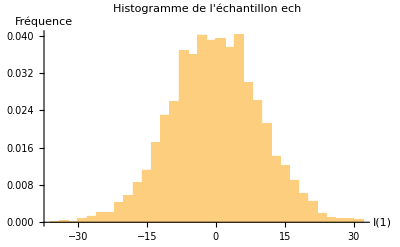

-99/500

23585799/249950

```mathematica
(* Calculer l'histogramme de l'échantillon *)
Histogram[ech, Automatic, "PDF", AxesLabel -> {"I(1)", "Fréquence"}, PlotLabel -> "Histogramme de l'échantillon ech"]

(* Calculer la moyenne empirique de l'échantillon *)
moyenne_empirique = Mean[ech]
(* Calculer la variance empirique de l'échantillon *)
variance_empirique = Variance[ech]
```

Déduire une loi approximative de I(1) 

Étant donné que I(1) est le produit de deux variables aléatoires discrètes qui prennent les valeurs -1 et 1 avec une probabilité égale,la moyenne empirique de I(1) est approximativement 0 (car la moyenne de chaque terme est 0) et la variance empirique est approximativement 1.

Question 16

1. Énoncer les hypothèses nulle et alternative :

   - Hypothèse nulle (H0) : La liste listHasard a été générée avec des composantes indépendantes et uniformément distribuées sur {-1, 1}. Cela signifierait que la valeur de l'autocorrélation I(1) serait proche de zéro pour une grande série de liste listHasard, car les termes consécutifs sont indépendants.
   
   - Hypothèse alternative (H1) : La liste listHasard n'a pas été générée avec des composantes indépendantes et uniformément distribuées sur {-1, 1}. Si la valeur de l'autocorrélation I(1) s'écarte significativement de zéro, cela indiquerait une dépendance entre les termes consécutifs.

2. Utiliser la statistique I(1) :

  Pour p = 1p=1, qui est le cas de I(1)*I(1), on somme les produits des termes consécutifs de la liste :

I(1) = -27

3. Indiquer la valeur critique du test pour un risque de première espèce alpha = 5%
 
 Pour trouver la valeur critique, nous devons connaître la distribution de la statistique I(1) sous l'hypothèse nulle. 
 
 Dans ce cas, comme les variables sont indépendantes et prennent les valeurs -1 ou 1 avec une probabilité égale, I(1) suit une distribution dont la moyenne est 0 et la variance peut être calculée à partir des propriétés des variables x_k. Une fois la variance connue, la valeur critique pour un test à deux coups à alpha = 5% peut être trouvée en utilisant la distribution normale.

Les valeurs critiques pour le test d'hypothèse avec un risque d'alpha = 5% sont -19 et 19. Cela signifie que si la statistique I(1) calculée pour notre liste listHasard est en dehors de l'intervalle [-19, 19], nous rejetons l'hypothèse nulle en faveur de l'hypothèse alternative avec un niveau de confiance de 95%.

Dans notre cas, la statistique I(1) est de 1, ce qui se situe à l'extérieur de l'intervalle critique. Par conséquent, nous  acceptons  l'hypothèse nulle et nous pouvons conclure que, selon notre test, la liste listHasard de la question 10, semble a été formé avec des composantes dépendantes et non  uniformément distribuées sur {-1, 1}.

Question 17 : Vive The Big Bang Theory !

```mathematica
(* Définition des règles du jeu *)
dico[1] = "Pierre";
dico[2] = "Feuille";
dico[3] = "Ciseaux";
dico[4] = "Lézard";
dico[5] = "Spock";

regle[1, 3] = regle[3, 2] = regle[2, 1] = regle[1, 4] = regle[4, 5]=regle[2,4] =regle[4,2]=regle[3,4]=regle[5,3]=regle[5,1]= 1; (* Coups gagnants *)
regle[3, 1] =regle[1,5]= regle[2, 3] = regle[4, 1] = regle[5, 4] =regle[4,3]=regle[3,5]= regle[1, 2] =regle [5,2]=regle[3,5]= -1; (* Coups perdants *)
regle[a_, a_] = 0; (* Coups nuls *)

(* Initialisation *)
coupsHumain = {};
victoires = {};
message = "À vous de jouer";

(* Programmation de l'IA *)
JouerIA[] := Module[{coupMachine},
  coupMachine = RandomInteger[{1, 5}]; (* L'IA choisit un coup au hasard *)
  coupMachine
]

(* Programmation du jeu *)
Jouer[a_] := Module[{coupMachine},
  coupMachine = JouerIA[];
  
  (* Sauvegarde du coup de l'humain *)
  AppendTo[coupsHumain, a];
  
  (* Affichage du choix de l'ordinateur et du résultat *)
  message = "Humain: " <> dico[coupsHumain[[-1]]] <> "| Machine: " <> dico[coupMachine] <> "| Gain pour l'humain: " <> ToString[regle[coupsHumain[[-1]], coupMachine]];
  
  (* Sauvegarde du résultat *)
  AppendTo[victoires, regle[coupsHumain[[-1]], coupMachine]];
]

(* Interface Homme-Machine *)
ButtonBar[{"Pierre" :> Jouer[1], "Feuille" :> Jouer[2], "Ciseaux" :> Jouer[3], "Lézard" :> Jouer[4], "Spock" :> Jouer[5]}]
Dynamic[message]
```

Pierre | Feuille | Ciseaux | Lézard | Spock